```mathematica
s[n_]:=Module[{mat},
mat=ConstantArray[0,{n,n}];
For[i=1,i≤n,i++,
For[j=i,j≤n,j++,
mat[[i,j]]=1.
];
];
(* Normalization
For[j=1,j≤n,j++,
mat[[All,j]]=mat[[All,j]]/Norm[mat[[All,j]]];
];
*)
mat
];
cond[mat_]:=Module[{n,sval},
sval=SingularValueList[mat];
n=Length[sval];
sval[[1]]/sval[[n]]
];
```

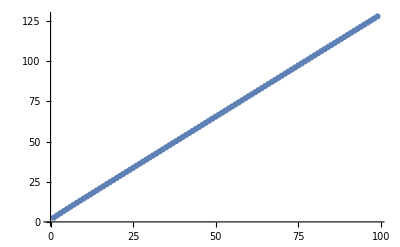

```mathematica
ListPlot[Table[cond[s[n]],{n,2,100}]]
```

```mathematica
MatrixForm[s[3]]
```

(1. | 1. | 1.
0 | 1. | 1.
0 | 0 | 1.)